## Redes de flat band system (saw-tooth chain)

```mathematica
t1= Sqrt[2]
t2= 1
```

√2

1

```mathematica
hamilt= ({{0, t1+t1 Exp[-I k]}, {t1 +t1 Exp[I k], 2 t2 Cos[k]}})
```

{{0,√2+√2 ⅇ^(-ⅈ k)},{√2+√2 ⅇ^(ⅈ k),2 Cos[k]}}

```mathematica
val=Eigenvalues[hamilt]
```

{-2,ⅇ^(-ⅈ k) (1+ⅇ^(ⅈ k))^2}

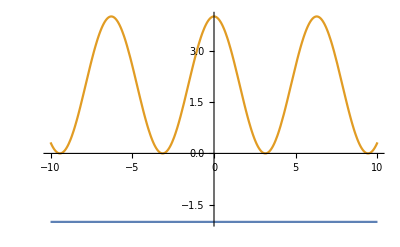

```mathematica
Plot[val,{k,-10,10}]
```